## Testing HW 4

### EXECUTE these cells first - say NO to ‘automatically evaluate all initialization cells’

#### code - find correct function names - general

```mathematica
(* find function names existing in kernel which matches the given pattern *)findPossibleName[functionName_,pattern_] := Module[{possibleNames,distances ,bestMatch ,x},
possibleNames= Names[pattern];
distances = Table[{item, EditDistance[item, functionName]},{item, possibleNames}];
bestMatch=possibleNames[[Flatten[Position[x=Table[Part[item,2], {item, distances}];x, Min[x] ]]]];
If [Length[bestMatch] < 1
, Return[]];
Return[bestMatch[[1]]]
]
```

```mathematica
(* replace first letter and each capital letter by an asterix *)
nameToPattern[funName_] :=StringReplace[StringReplacePart[funName, "*", {1,1}], CharacterRange["A", "Z"] -> "*"]
```

```mathematica
(* find function names existing in kernel which are close to given funcction name; first letter and capital letters are made 'variable' *)
findPossibleName[functionName_] := 
Return[findPossibleName[functionName, nameToPattern[functionName]]];
```

```mathematica
(* find the actual function to call which has a name close to the given name *)
findFunction[functionName_, pattern_, display_] := Module[{useName = functionName, useThis},
If[!NameQ[functionName]
		, Print[Style[StringJoin["     ERROR - no function with name ", functionName, " exists"], Red]];
		    useName= findPossibleName[functionName, pattern];
		     If [useName == Null 
		       , If[display
			, Print[Style["            no suitable replacement found to use ", Red]];
			     Print[Style["            evaluation of function ", functionName, " failed completely", Red]];
			];
			Return[];
		];
];
(* execute the function *)
  If [useName == functionName && display
, Print["function ", functionName, " exists and is used "];
Return[{True, useName}];
,  Print[Style[StringJoin["     ATTEMPTING to use ", useName, " for the test"], Blue]];
Return[{False, useName}];
]	
(*Return[{True,useName}]*)
]
```

```mathematica
(* find the actual function to call which has a name close to the given function name *)
findFunction[functionName_,  display_] := 
  findFunction[functionName, nameToPattern[functionName], display]
```

```mathematica
testFunctionExists[funName_, formalLst_, paramLst_,  pattern_]:=Module [
{foundNames, useFunName,(* useThis,*) res, useThisStr},
(* find a suitably close function name to use *)
foundNames=findFunction[funName, pattern, True]; 
 If[ Length[foundNames] == 0,
	Return[ {StringJoin ["Result for "  <> funName <> ": "], Style[" FUNCIONT DOES NOT EXIST",Red]}]
];	
If[! SameQ[funName,foundNames[[2]]],
Return[ {"Result for "  <> funName <> ": ", Style["MISSPELLED name to " <> foundNames[[2]] <> "?",Red]}]
];
 useFunName = foundNames[[2]];

(* create the funcion to see whether it exists ... *)
 useThisStr = StringJoin["useThis [",
			StringRiffle[formalLst, {"", "_, ", "_"}],
			"] := Apply [ Symbol [ \"", useFunName,
			"\"] , ",
			StringRiffle[formalLst, {"{",", ", "}"}],
			" ]"
			];
(*Print[" XXXX"<>useThisStr<>"XXX"];*)
Clear[useThis];
ToExpression[useThisStr]; (* this creates the function as
						if the above string had been typed in *)

(* excute the function and report the result... *)
 res = {"Result for "  <> useFunName <> ": ", paramLst,
Check[ 
TimeConstrained[ Apply [useThis, paramLst], 1, Style["EXECUTION TOOK TOO LONG ", Red]
] , Style[" EXECUTION CAUSED AN EXCEPTION ",Red]
]}
]
```

```mathematica
testFunctionExists[funName_, formalLst_, paramLst_]:=
(* find the actual function to use which has a name close to the given function name *)
testFunctionExists[funName,  formalLst, paramLst, nameToPattern[funName]]
```

#### code - verify return type - general

```mathematica
verifyReturnTypeAndStructure[result_, {correctType_, correctStructure_}] := Module[
{correctTypes, errorMsg},
If [!SameQ[Head[result], correctType],
	errorMsg =Style[StringJoin["Error - incorrect type returned; should be a ", ToString[correctType]], Red];
	Print[errorMsg];
	Return[False]
];
If[correctType === List,
(* check type of each list element in result against correctStructure type *)
If[SameQ[correctStructure[[1]] ,"individual"],
(* types in list might be different *)
correctTypes =Table[SameQ[Head[result[[i]]], Head[correctStructure[[2,i]]]],{i, 1, Length[correctStructure[[2]]]}];
(*Print["correctStructure ", correctStructure, " correctypes " ,correctTypes, " ", Table[Head[result[[i]]],{i, 1, Length[correctStructure[[2]]]}], " ",
Table[Head[correctStructure[[2,i]]],{i, 1, Length[correctStructure[[2]]]}]];*)
If [! Apply[And,correctTypes],
	errorMsg=Style["Error - incorrect types of list elements in result", Red];
	Print[errorMsg];
	Return[False]
 ];,
    (* else - not individual structure 
all elements should have the same structure as the one given *)
 Print["repetitive structures are NOT INCLUDED SO FAR INTO TESTING HARNESS"];
];
Print[Style["Correct types", Blue]];
Return[True];
];
Print[Style["Correct types", Blue]];
Return[True]
]
```

#### pointlist checking code: i) verify length of list, ii) verify x values

```mathematica
(* checks whether result lst has the correct length and evenly spaced x-values *)
checkFuncPointLengthRange[resultLst_, targetLength_]:=Module[
{},
(* is length correct and x-axis spacing*)
If [checkFuncPointLength[resultLst, targetLength] && checkFuncPointRange[resultLst] ,
Return[True]
];
Return[False]
]
```

```mathematica
(* checks whether result lst has the correct length  *)
checkFuncPointLength[resultLst_, targetLength_]:=Module[
{distanceLst,distanceDiff},
(* is length to be checked - and is condition failed? *)
If [targetLength > 0 && Length[resultLst] ≠ targetLength,
Print[Style[StringJoin[ "Incorrect length of result: is ", 
					ToString[Length[resultLst]], " instead of " ,
					ToString[ targetLength]],Red]];
Return[False]
];
Return[True]
]
```

```mathematica
(* checks whether result lst has evenly spaced x-values *)
checkFuncPointRange[resultLst_]:=Module[
{distanceLst,distanceDiff},
(* are x-values evenly spaced? *)
distanceLst=Table[EuclideanDistance[resultLst[[i,1]], resultLst[[i-1,1]]],{i, 2, Length[resultLst]}];
distanceDiff =Chop[ Abs[distanceLst - distanceLst[[1]]]];
If [ Total[distanceDiff]/Length[resultLst] > 10^-5,
Print[Style[ "Incorrect x-values: not evenly spaced"],Red];
Return[False]
];
Return[True]
]
```

```mathematica
testfindPoints[ correctAnswer_, studentRes_, precision_]:= 
Module[{ sum},
(* now check actual results *)
If[ Max[Table[EuclideanDistance[studentRes[[i]], correctAnswer[[i]]],{i, 1, Length[studentRes]}]] > 10^-precision,
Print [Style["Incorrect results; " <> ToString[studentRes], Red]];
Return[False]
];
Return[True]
];
```

#### verticalTrace checking code: i) verify maxBlanks, minBlanks, ii) verify blanks to scale

```mathematica
(* checks whether result lst has at least one entry with maxBlanks leading blanks and 1 entry with 0 leading blanks *)
checkVerticalTraceMinMaxBlanks[resultLst_, maxBlanks_, text_]:=Module[
{leadingBlanksLst={}, textBlanks = StringCount[text, " "]},
(* count leading blanks - assumes no trailing blanks *)
leadingBlanksLst = Table[StringCount[item, " "]- textBlanks, {item, resultLst}];
If [! MemberQ[leadingBlanksLst, maxBlanks],   
  Print[ Style[StringJoin[ "Incorrect - no line with " , ToString[ maxBlanks] <> " leading blanks "],Red]];
  Return [False]
];
If [! MemberQ[leadingBlanksLst, 0],
  Print[ Style[StringJoin[ "Incorrect - no line with 0 leading blanks "],Red]];
  Return [False]
];
Return[True]
]
```

```mathematica
(* checks whether leading blanks are in line with  *)
checkVerticalTraceBlankCount[studentResult_, correctResult_, text_]:=Module[
{studentLeadingBlanksLst={},correctLeadingBlanksLst={}, textBlanks = StringCount[text, " "], diff},
(* count leading blanks - assumes no trailing blanks *)
studentLeadingBlanksLst = Table[StringCount[item, " "]- textBlanks, {item, studentResult}];
correctLeadingBlanksLst = Table[StringCount[item, " "]- textBlanks, {item, correctResult}];
Print["leading Blnaks lists stud, corr", studentLeadingBlanksLst, " ", correctLeadingBlanksLst];
diff= Table[studentLeadingBlanksLst[[i]] - correctLeadingBlanksLst[[i]],{i, 1, Length[correctLeadingBlanksLst]}];
If [Max[Abs[diff]]> 1,
  Print[ Style[StringJoin[ "Incorrect - incorrect number of leading blanks "],Red]];
  Return [False]
];
If [Total[diff]> 2,
  Print[ Style[StringJoin[ "Incorrect - number of leading blanks off too often "],Red]];
  Return [False]
];
Return[True]
]
```

```mathematica
checkVerticalTrace[ correctAnswer_, studentRes_, maxBlanks_, text_]:= 
Module[{ sum},
 (* check max and min blanks  *)
If[! checkVerticalTraceMinMaxBlanks[studentRes, maxBlanks, text],
Return[False]
];
(* check scaled blanks *)
If[! checkVerticalTraceBlankCount[studentRes, correctAnswer, text],
Return[False]
];
Return[True]
];
```

#### data needed -- execute this cell

```mathematica
test1={{{0.,0.},{0.5711986642890533,0.16313395704279932},{1.1423973285781066,0.6525358281711973},{1.7135959928671598,1.4682056133851935},{2.284794657156213,2.610143312684789},{2.855993321445266,4.078348926069982},{3.4271919857343196,5.872822453540774},{3.998390650023373,7.993563895097166},{4.569589314312426,10.440573250739156},{5.14078797860148,13.213850520466746},{5.711986642890532,16.313395704279927},{6.283185307179586,19.739208802178716}},{{-3.141592653589793,4.934802200544679},{-2.8108986900540254,3.950575722873718},{-2.4802047265182576,3.0757077427217525},{-2.14951076298249,2.3101982600887827},{-1.8188167994467224,1.6540472749748094},{-1.4881228359109546,1.107254787379831},{-1.1574288723751869,0.6698207973038484},{-0.8267349088394192,0.34174530474686143},{-0.4960409453036515,0.12302830970887009},{-0.16534698176788384,0.013669812189874456},{0.16534698176788384,0.013669812189874456},{0.4960409453036515,0.12302830970887009},{0.8267349088394192,0.34174530474686143},{1.1574288723751869,0.6698207973038484},{1.4881228359109546,1.107254787379831},{1.8188167994467224,1.6540472749748094},{2.14951076298249,2.3101982600887827},{2.4802047265182576,3.0757077427217525},{2.8108986900540254,3.950575722873718},{3.141592653589793,4.934802200544679}},{{-1.5,-4.470462379180405},{1.,0.3095598756531122},{3.5,-0.010592735624661903}},{{-1.5,-4.470462379180405},{-1.236842105263158,-3.2544099772757042},{-0.9736842105263158,-2.189533779434537},{-0.7105263157894737,-1.327334264707414},{-0.44736842105263164,-0.6766600912863991},{-0.1842105263157896,-0.22022016530995472},{0.07894736842105265,0.07287859995140376},{0.3421052631578947,0.23827620938970986},{0.6052631578947367,0.3106228569921079},{0.8684210526315788,0.3202951691429742},{1.1315789473684208,0.2919111928367331},{1.3947368421052628,0.2440661341459539},{1.6578947368421053,0.1898174213911453},{1.9210526315789473,0.1375608133708572},{2.1842105263157894,0.0920442590042643},{2.4473684210526314,0.05535520337838258},{2.7105263157894735,0.027787099353248138},{2.973684210526316,0.008542308953687688},{3.2368421052631575,-0.003736482340406942},{3.5,-0.010592735624661903}}};
```

```mathematica
test2={{Text["1",{0.,0.}],Text["2",{0.5711986642890533,0.16313395704279932}],Text["3",{1.1423973285781066,0.6525358281711973}],Text["4",{1.7135959928671598,1.4682056133851935}],Text["5",{2.284794657156213,2.610143312684789}],Text["6",{2.855993321445266,4.078348926069982}],Text["7",{3.4271919857343196,5.872822453540774}],Text["8",{3.998390650023373,7.993563895097166}],Text["9",{4.569589314312426,10.440573250739156}],Text["0",{5.14078797860148,13.213850520466746}],Text["1",{5.711986642890532,16.313395704279927}],Text["2",{6.283185307179586,19.739208802178716}]},{Text["T",{-3.141592653589793,4.934802200544679}],Text["h",{-2.8108986900540254,3.950575722873718}],Text["e",{-2.4802047265182576,3.0757077427217525}],Text["r",{-2.14951076298249,2.3101982600887827}],Text["e",{-1.8188167994467224,1.6540472749748094}],Text[" ",{-1.4881228359109546,1.107254787379831}],Text["a",{-1.1574288723751869,0.6698207973038484}],Text["r",{-0.8267349088394192,0.34174530474686143}],Text["e",{-0.4960409453036515,0.12302830970887009}],Text[" ",{-0.16534698176788384,0.013669812189874456}],Text["2",{0.16534698176788384,0.013669812189874456}],Text["0",{0.4960409453036515,0.12302830970887009}],Text[" ",{0.8267349088394192,0.34174530474686143}],Text["l",{1.1574288723751869,0.6698207973038484}],Text["e",{1.4881228359109546,1.107254787379831}],Text["t",{1.8188167994467224,1.6540472749748094}],Text["t",{2.14951076298249,2.3101982600887827}],Text["e",{2.4802047265182576,3.0757077427217525}],Text["r",{2.8108986900540254,3.950575722873718}],Text["s",{3.141592653589793,4.934802200544679}]},{Text["C",{-1.5,-4.470462379180405}],Text["S",{1.,0.3095598756531122}],Text["P",{3.5,-0.010592735624661903}]},{Text["h",{-1.5,-4.470462379180405}],Text["o",{-1.236842105263158,-3.2544099772757042}],Text["r",{-0.9736842105263158,-2.189533779434537}],Text["i",{-0.7105263157894737,-1.327334264707414}],Text["z",{-0.44736842105263164,-0.6766600912863991}],Text["o",{-0.1842105263157896,-0.22022016530995472}],Text["n",{0.07894736842105265,0.07287859995140376}],Text["t",{0.3421052631578947,0.23827620938970986}],Text["a",{0.6052631578947367,0.3106228569921079}],Text["l",{0.8684210526315788,0.3202951691429742}],Text[" ",{1.1315789473684208,0.2919111928367331}],Text["t",{1.3947368421052628,0.2440661341459539}],Text["r",{1.6578947368421053,0.1898174213911453}],Text["a",{1.9210526315789473,0.1375608133708572}],Text["c",{2.1842105263157894,0.0920442590042643}],Text["e",{2.4473684210526314,0.05535520337838258}]}};
```

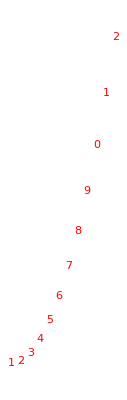
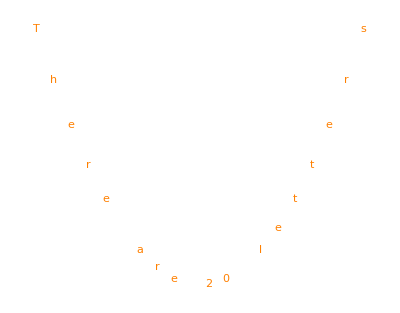
```mathematica
test3={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

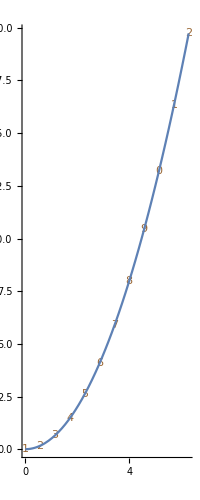
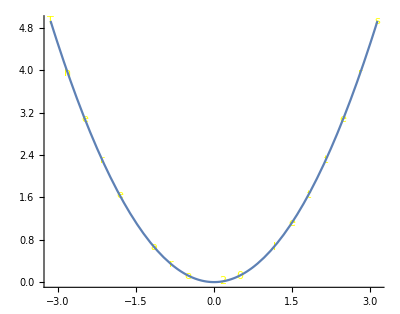
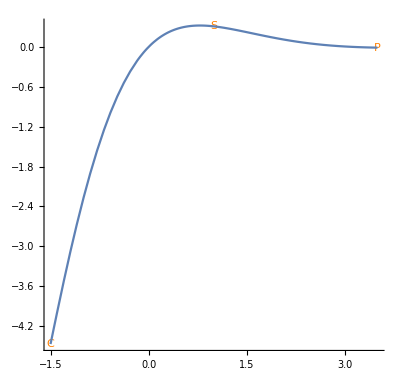
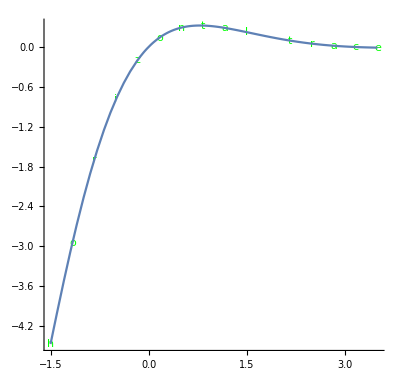
```mathematica
test4={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
test5={{{"  Parabola"},{" Parabola"},{"Parabola"},{"Parabola"},{" Parabola"},{"   Parabola"},{"      Parabola"},{"          Parabola"}},{{"          Cos"},{"        Cos"},{"    Cos"},{"Cos"},{"Cos"},{"    Cos"},{"        Cos"},{"          Cos"}},{{"        CPS"},{"            CPS"},{"               CPS"},{"               CPS"},{"           CPS"},{"       CPS"},{"  CPS"},{"CPS"},{" CPS"},{"     CPS"}},{{"x^2"},{" x^2"},{"  x^2"},{"   x^2"},{"     x^2"},{"      x^2"},{"        x^2"},{"          x^2"},{"             x^2"},{"               x^2"}}};
```

### Text display problem - basic testing

#### testing whether all functions exist and can be executed -

Execute this cell!!!

```mathematica
funNameLstTextDisplayRaw = {
hw4createPointLst, 
hw4prepareTextDisplay,
hw4displayText,
hw4horizontalTrace,
hw4verticalTrace};
```

```mathematica
formalParamlstTextDisplayRaw={
{ hw4func, hw4lower, hw4upper, hw4points}, 
{ hw4text, hw4pointlist, hw4color},
{ hw4primitiveLst},
{ hw4func, hw4text,hw4lower, hw4upper, hw4color},
{ hw4func, hw4text, hw4lines, hw4lower, hw4upper, hw4maxBlanks}
};
```

```mathematica
funNameLstTextDisplay=Table[StringDrop[ToString[item],3],{item, funNameLstTextDisplayRaw}];
```

```mathematica
Table[ToExpression["Remove["<>ToString[item]<>"]"],{item, funNameLstTextDisplayRaw}];
```

```mathematica
formalParamlstTextDisplay=
Table [
	Table [ToString[item],{item, blah}],
	{blah, formalParamlstTextDisplayRaw}
];
```

```mathematica
actualParamlstTextDisplay = { 
{hw4gfun,-1.5, 3.5, 16},
{"HW4 tes", {{0,0},{0.3, 0},{0.6,0.2},{1.2,0.9},{1.5, 0.3}, {2, -.8}, {2.5, -1.9}}, Orange},
{{Text["G",{0,0}],Text["a",{0.3,0}],Text["t",{0.6,0.2}],Text["t",{1.2,0.9}],Text["o",{1.5,0.3}],Text["n",{2,-0.8}]}},
{hw4gfun, "HW4 test",-1.5, 3.5,Purple},
{hw4ffun, "HW4 test 2",12, -1.5, 3.5, 10}
};
```

```mathematica
hw4gfun[x_]:=  Cos[x]
hw4ffun[x_]:= 0.5 x^2
hw4hfun[x_] :=  E^-x Sin[x]
```

function createPointLst exists and is used

function prepareTextDisplay exists and is used

function displayText exists and is used

function horizontalTrace exists and is used

function verticalTrace exists and is used

HW4 test 2

HW4 test 2

HW4 test 2

«9 more identical outputs»

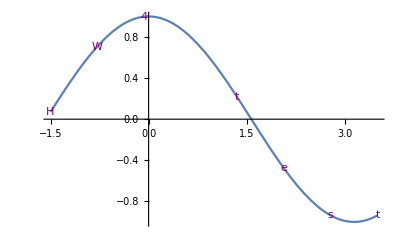
Result for createPointLst:  | {hw4gfun,-1.5,3.5,16} | {{-1.5,0.0707372},{-1.16667,0.393219},{-0.833333,0.672412},{-0.5,0.877583},{-0.166667,0.986143},{0.166667,0.986143},{0.5,0.877583},{0.833333,0.672412},{1.16667,0.393219},{1.5,0.0707372},{1.83333,-0.259531},{2.16667,-0.561229},{2.5,-0.801144},{2.83333,-0.952863},{3.16667,-0.999686},{3.5,-0.936457}}
Result for prepareTextDisplay:  | {HW4 tes,{{0,0},{0.3,0},{0.6,0.2},{1.2,0.9},{1.5,0.3},{2,-0.8},{2.5,-1.9}},RGBColor[1, 0.5, 0]} | {Text[H,{0,0}],Text[W,{0.3,0}],Text[4,{0.6,0.2}],Text[ ,{1.2,0.9}],Text[t,{1.5,0.3}],Text[e,{2,-0.8}],Text[s,{2.5,-1.9}]}
Result for displayText:  | {{Text[G,{0,0}],Text[a,{0.3,0}],Text[t,{0.6,0.2}],Text[t,{1.2,0.9}],Text[o,{1.5,0.3}],Text[n,{2,-0.8}]}} | -Graphics-
Result for horizontalTrace:  | {hw4gfun,HW4 test,-1.5,3.5,RGBColor[0.5, 0, 0.5]} | -Graphics-
Result for verticalTrace:  | {hw4ffun,HW4 test 2,12,-1.5,3.5,10} |

```mathematica
(* testing each function - name and simple execution *)
Module[
{i},
Grid[
Table[testFunctionExists[funNameLstTextDisplay[[i]], formalParamlstTextDisplay[[i]], actualParamlstTextDisplay[[i]]],
 {i, 1,  Length[funNameLstTextDisplay]}
],
Frame->All
]
]
```

#### testing return type of all functions

execute this cell

```mathematica
correctTypeLstTextDisplay = { 
{List, {"individual",{ {1,2}, {1,2}, {1,2}}}},  
{List, {"individual",{Text["here"], Text["there"]}}},
{Graphics, {}},
{Graphics, {}},
{Symbol, {}}
};
```

```mathematica
Module[{testResult,i},
TableForm[Table[
Print["processing: " ,funNameLstTextDisplay[[i]]]; testResult=Apply[ToExpression[funNameLstTextDisplay[[i]]], actualParamlstTextDisplay[[i]]];
{funNameLstTextDisplay[[i]],verifyReturnTypeAndStructure[testResult,  correctTypeLstTextDisplay[[i]]]},
 {i, 1, Length[funNameLstTextDisplay]}
]
]
]
```

processing: createPointLst

Correct types

processing: prepareTextDisplay

Correct types

processing: displayText

Correct types

processing: horizontalTrace

Correct types

processing: verticalTrace

HW4 test 2

HW4 test 2

HW4 test 2

«9 more identical outputs»

Correct types

createPointLst | True
prepareTextDisplay | True
displayText | True
horizontalTrace | True
verticalTrace | True

### TextDisplay problem - individual functions

#### Code testing functions - TextDisplay -- EXCUTE cell AFTER basic testing for TextDisplay

```mathematica
testfindPoints[ correctAnswer_, studentRes_, precision_]:= 
Module[{ sum},
(* now check actual results *)
If[ Max[Table[EuclideanDistance[studentRes[[i]], correctAnswer[[i]]],{i, 1, Length[studentRes]}]] > 10^-precision,
Print [Style["Incorrect results; " <> ToString[studentRes], Red]];
Return[False]
];
Return[True]
];
```

```mathematica
testCreatePointLst[testCases_, test_]:=Module [
{func, low, upp, points,res,checkRes, i=1},
Grid[
Table[
SeedRandom[201];
func=item[[1]];
low=item[[2]];
upp=item[[3]];
points=item[[4]];
res = Check[ 
TimeConstrained[ createPointLst[ func,low,upp,points], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={createPointLst, {func,low,upp,points}, res},
(* else *)
	   checkRes={createPointLst,  {func,low,upp,points}, checkFuncPointLengthRange[res, points] && testfindPoints[test[[i]],res, 5]}
];
i++;
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testPrepareTextDisplay[testCases_, test_]:=Module [
{text, ptLst, color, res,checkRes, i=1},
Grid[
Table[
text=item[[1]];
ptLst=item[[2]];
color=item[[3]];
res = Check[ 
TimeConstrained[ prepareTextDisplay[text, ptLst, color], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={prepareTextDisplay,{text, ptLst, color}, res},
(* else *)
          If[!checkFuncPointLength[res, StringLength[text]],
        checkRes={prepareTextDisplay,  {text, ptLst, color}, res},
	(*else *)
       checkRes={prepareTextDisplay,   {text, ptLst, color}, {test[[i]]," < -- Correct COMPARE TO Student -->", res } }
      ];
];
i++;
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testDisplayText[testCases_, test_]:=Module [
{text, primitiveLst, color, res,checkRes, i=1},
Grid[
Table[
primitiveLst=item;
res = Check[ 
TimeConstrained[ displayText[primitiveLst], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={displayText,{primitiveLst}, res},
(* else *)
            checkRes={displayText,   {primitiveLst}, {test[[i]]," < -- Correct COMPARE TO Student -->", res } }
];
i++;
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
testHorizontalTrace[testCases_, test_]:=Module [
{fun,text, low, up, col, res,checkRes, i=1},
Grid[
Table[
fun = item[[1]];
text=item[[2]];
low= item[[3]];
up = item[[4]];
col = item[[5]];
res = Check[ 
TimeConstrained[ horizontalTrace[fun, text, low, up, col], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={horizontalTrace,{fun, text, low, up, col}, res},
(* else *)
            checkRes={horizontalTrace,   {fun, text, low, up, col}, {test[[i]]," < -- Correct COMPARE TO Student -->", res } }
];
i++;
checkRes,
{item, testCases}
],
Frame->All
]
]
```

```mathematica
captureResult[paramLst_] := Module[
{res ={}},
Block[{Print=AppendTo[res,{##}]&},Apply[verticalTrace, paramLst]];
Return[res]
]
```

```mathematica
displayPrint[lst_]:=StringJoin[StringRiffle[ Flatten[lst], "\n"]]
```

```mathematica
testVerticalTrace[testCases_, test_]:=Module [
{fun,text, low, up, lines, mxBl, res,checkRes, i=1, uzi,k},
Grid[
Table[
fun = item[[1]];
text=item[[2]];
lines=item[[3]];
low= item[[4]];
up = item[[5]];
mxBl = item[[6]];
res = Check[ 
TimeConstrained[ verticalTrace[fun, text,lines, low, up, mxBl], 10, Style["EXECUTION TOOK TOO LONG ", Red]] , 
Style[" EXECUTION CAUSED AN EXCEPTION ",Red]];

  If[SameQ[res, "EXECUTION TOOK TOO LONG "] || SameQ[res, " EXECUTION CAUSED AN EXCEPTION "],
            checkRes={verticalTrace,{fun, text,lines, low, up, mxBl}, res},
(* else *)
	       (* capture the result for checking *)
                 res=captureResult[{fun, text, lines, low, up, mxBl}];
	        If[!checkVerticalTrace[ Flatten[test[[i]]], Flatten[res], mxBl, text],
                     checkRes={prepareTextDisplay,  {fun, text,lines, low, up, mxBl}, res},
		     (* else *)
	            checkRes={verticalTrace,   {fun, text,lines, low, up, mxBl}, {"\n"<>displayPrint[test[[i]]] <>"\n < -- Correct COMPARE TO Student -->\n" <> displayPrint[res] } }
             ];
];
i++;
checkRes,
{item, testCases}
],
Frame->All
]
]
```

#### testing return values - for students createPointLst

```mathematica
hw4gfun[x_]:=  Cos[x]
hw4ffun[x_]:= 0.5 x^2
hw4hfun[x_] :=  E^-x Sin[x]
hw4kfun[x_]:= Sin[x]
hw4mfun[x_]:= 3 x^2
```

```mathematica
(* this is a list for the parameters for each of the funtion calls made during the test *)testCreatePointLstCases= {{hw4ffun, 0,  2 π, 12}, {hw4ffun, -π,   π, 20},{hw4hfun, -1.5,  3.5, 3},{hw4hfun, -1.5,  3.5, 20}};
```

```mathematica
(* displays True in the last column if your answers were reasonably close to the expected answers *)
testCreatePointLst[testCreatePointLstCases, test1]
```

createPointLst | {hw4ffun,0,2 π,12} | True
createPointLst | {hw4ffun,-π,π,20} | True
createPointLst | {hw4hfun,-1.5,3.5,3} | True
createPointLst | {hw4hfun,-1.5,3.5,20} | True

#### testing return values - for students prepareTextDisplay

```mathematica
hw4gfun[x_]:=  Cos[x]
hw4ffun[x_]:= 0.5 x^2
hw4hfun[x_] :=  E^-x Sin[x]
```

```mathematica
(* this is a list for the parameters for each of the funtion calls made during the test *)testPrepareTextDisplayCases= {{ "123456789012", test1[[1]], Red}, {"There are 20 letters", test1[[2]], Orange},{"CSP", test1[[3]], Blue},{"horizontal trace", test1[[4]], Black}};
```

```mathematica
(* since there are many different ways of accomplishing the required work most tests will not work for all solutions*)
(* in addition to the internal testing a visual comparison is needed to determine whether the items are the same *)
testPrepareTextDisplay[testPrepareTextDisplayCases, test2]
```

prepareTextDisplay | {123456789012,{{0.,0.},{0.571199,0.163134},{1.1424,0.652536},{1.7136,1.46821},{2.28479,2.61014},{2.85599,4.07835},{3.42719,5.87282},{3.99839,7.99356},{4.56959,10.4406},{5.14079,13.2139},{5.71199,16.3134},{6.28319,19.7392}},RGBColor[1, 0, 0]} | {{Text[1,{0.,0.}],Text[2,{0.571199,0.163134}],Text[3,{1.1424,0.652536}],Text[4,{1.7136,1.46821}],Text[5,{2.28479,2.61014}],Text[6,{2.85599,4.07835}],Text[7,{3.42719,5.87282}],Text[8,{3.99839,7.99356}],Text[9,{4.56959,10.4406}],Text[0,{5.14079,13.2139}],Text[1,{5.71199,16.3134}],Text[2,{6.28319,19.7392}]}, < -- Correct COMPARE TO Student -->,{Text[1,{0.,0.}],Text[2,{0.571199,0.163134}],Text[3,{1.1424,0.652536}],Text[4,{1.7136,1.46821}],Text[5,{2.28479,2.61014}],Text[6,{2.85599,4.07835}],Text[7,{3.42719,5.87282}],Text[8,{3.99839,7.99356}],Text[9,{4.56959,10.4406}],Text[0,{5.14079,13.2139}],Text[1,{5.71199,16.3134}],Text[2,{6.28319,19.7392}]}}
prepareTextDisplay | {There are 20 letters,{{-3.14159,4.9348},{-2.8109,3.95058},{-2.4802,3.07571},{-2.14951,2.3102},{-1.81882,1.65405},{-1.48812,1.10725},{-1.15743,0.669821},{-0.826735,0.341745},{-0.496041,0.123028},{-0.165347,0.0136698},{0.165347,0.0136698},{0.496041,0.123028},{0.826735,0.341745},{1.15743,0.669821},{1.48812,1.10725},{1.81882,1.65405},{2.14951,2.3102},{2.4802,3.07571},{2.8109,3.95058},{3.14159,4.9348}},RGBColor[1, 0.5, 0]} | {{Text[T,{-3.14159,4.9348}],Text[h,{-2.8109,3.95058}],Text[e,{-2.4802,3.07571}],Text[r,{-2.14951,2.3102}],Text[e,{-1.81882,1.65405}],Text[ ,{-1.48812,1.10725}],Text[a,{-1.15743,0.669821}],Text[r,{-0.826735,0.341745}],Text[e,{-0.496041,0.123028}],Text[ ,{-0.165347,0.0136698}],Text[2,{0.165347,0.0136698}],Text[0,{0.496041,0.123028}],Text[ ,{0.826735,0.341745}],Text[l,{1.15743,0.669821}],Text[e,{1.48812,1.10725}],Text[t,{1.81882,1.65405}],Text[t,{2.14951,2.3102}],Text[e,{2.4802,3.07571}],Text[r,{2.8109,3.95058}],Text[s,{3.14159,4.9348}]}, < -- Correct COMPARE TO Student -->,{Text[T,{-3.14159,4.9348}],Text[h,{-2.8109,3.95058}],Text[e,{-2.4802,3.07571}],Text[r,{-2.14951,2.3102}],Text[e,{-1.81882,1.65405}],Text[ ,{-1.48812,1.10725}],Text[a,{-1.15743,0.669821}],Text[r,{-0.826735,0.341745}],Text[e,{-0.496041,0.123028}],Text[ ,{-0.165347,0.0136698}],Text[2,{0.165347,0.0136698}],Text[0,{0.496041,0.123028}],Text[ ,{0.826735,0.341745}],Text[l,{1.15743,0.669821}],Text[e,{1.48812,1.10725}],Text[t,{1.81882,1.65405}],Text[t,{2.14951,2.3102}],Text[e,{2.4802,3.07571}],Text[r,{2.8109,3.95058}],Text[s,{3.14159,4.9348}]}}
prepareTextDisplay | {CSP,{{-1.5,-4.47046},{1.,0.30956},{3.5,-0.0105927}},RGBColor[0, 0, 1]} | {{Text[C,{-1.5,-4.47046}],Text[S,{1.,0.30956}],Text[P,{3.5,-0.0105927}]}, < -- Correct COMPARE TO Student -->,{Text[C,{-1.5,-4.47046}],Text[S,{1.,0.30956}],Text[P,{3.5,-0.0105927}]}}
prepareTextDisplay | {horizontal trace,{{-1.5,-4.47046},{-1.23684,-3.25441},{-0.973684,-2.18953},{-0.710526,-1.32733},{-0.447368,-0.67666},{-0.184211,-0.22022},{0.0789474,0.0728786},{0.342105,0.238276},{0.605263,0.310623},{0.868421,0.320295},{1.13158,0.291911},{1.39474,0.244066},{1.65789,0.189817},{1.92105,0.137561},{2.18421,0.0920443},{2.44737,0.0553552},{2.71053,0.0277871},{2.97368,0.00854231},{3.23684,-0.00373648},{3.5,-0.0105927}},GrayLevel[0]} | {{Text[h,{-1.5,-4.47046}],Text[o,{-1.23684,-3.25441}],Text[r,{-0.973684,-2.18953}],Text[i,{-0.710526,-1.32733}],Text[z,{-0.447368,-0.67666}],Text[o,{-0.184211,-0.22022}],Text[n,{0.0789474,0.0728786}],Text[t,{0.342105,0.238276}],Text[a,{0.605263,0.310623}],Text[l,{0.868421,0.320295}],Text[ ,{1.13158,0.291911}],Text[t,{1.39474,0.244066}],Text[r,{1.65789,0.189817}],Text[a,{1.92105,0.137561}],Text[c,{2.18421,0.0920443}],Text[e,{2.44737,0.0553552}]}, < -- Correct COMPARE TO Student -->,{Text[h,{-1.5,-4.47046}],Text[o,{-1.23684,-3.25441}],Text[r,{-0.973684,-2.18953}],Text[i,{-0.710526,-1.32733}],Text[z,{-0.447368,-0.67666}],Text[o,{-0.184211,-0.22022}],Text[n,{0.0789474,0.0728786}],Text[t,{0.342105,0.238276}],Text[a,{0.605263,0.310623}],Text[l,{0.868421,0.320295}],Text[ ,{1.13158,0.291911}],Text[t,{1.39474,0.244066}],Text[r,{1.65789,0.189817}],Text[a,{1.92105,0.137561}],Text[c,{2.18421,0.0920443}],Text[e,{2.44737,0.0553552}]}}

#### testing return values - for students displayText

```mathematica
(* this is a list for the parameters for each of the funtion calls made during the test *)testdisplayTextCases={test2[[1]], test2[[2]], test2[[3]], test2[[4]]};
```

```mathematica
(* since there are many different ways of accomplishing the required work most tests will not work for all solutions*)
(* a visual comparison is needed to determine whether the items are the same *)testDisplayText[testdisplayTextCases, test3]
```

displayText | {{Text[1,{0.,0.}],Text[2,{0.571199,0.163134}],Text[3,{1.1424,0.652536}],Text[4,{1.7136,1.46821}],Text[5,{2.28479,2.61014}],Text[6,{2.85599,4.07835}],Text[7,{3.42719,5.87282}],Text[8,{3.99839,7.99356}],Text[9,{4.56959,10.4406}],Text[0,{5.14079,13.2139}],Text[1,{5.71199,16.3134}],Text[2,{6.28319,19.7392}]}} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
displayText | {{Text[T,{-3.14159,4.9348}],Text[h,{-2.8109,3.95058}],Text[e,{-2.4802,3.07571}],Text[r,{-2.14951,2.3102}],Text[e,{-1.81882,1.65405}],Text[ ,{-1.48812,1.10725}],Text[a,{-1.15743,0.669821}],Text[r,{-0.826735,0.341745}],Text[e,{-0.496041,0.123028}],Text[ ,{-0.165347,0.0136698}],Text[2,{0.165347,0.0136698}],Text[0,{0.496041,0.123028}],Text[ ,{0.826735,0.341745}],Text[l,{1.15743,0.669821}],Text[e,{1.48812,1.10725}],Text[t,{1.81882,1.65405}],Text[t,{2.14951,2.3102}],Text[e,{2.4802,3.07571}],Text[r,{2.8109,3.95058}],Text[s,{3.14159,4.9348}]}} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
displayText | {{Text[C,{-1.5,-4.47046}],Text[S,{1.,0.30956}],Text[P,{3.5,-0.0105927}]}} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
displayText | {{Text[h,{-1.5,-4.47046}],Text[o,{-1.23684,-3.25441}],Text[r,{-0.973684,-2.18953}],Text[i,{-0.710526,-1.32733}],Text[z,{-0.447368,-0.67666}],Text[o,{-0.184211,-0.22022}],Text[n,{0.0789474,0.0728786}],Text[t,{0.342105,0.238276}],Text[a,{0.605263,0.310623}],Text[l,{0.868421,0.320295}],Text[ ,{1.13158,0.291911}],Text[t,{1.39474,0.244066}],Text[r,{1.65789,0.189817}],Text[a,{1.92105,0.137561}],Text[c,{2.18421,0.0920443}],Text[e,{2.44737,0.0553552}]}} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}

#### testing return values - for students horizontal trace

```mathematica
(* this is a list for the parameters for each of the funtion calls made during the test *)testHorizontalTraceCases={{hw4ffun, "123456789012", 0,  2 π, Brown}, {hw4ffun, "There are 20 letters", -π,   π, Yellow},{hw4hfun, "CSP", -1.5,  3.5, Orange},{hw4hfun,"horizontal trace",  -1.5,  3.5, Green}};
```

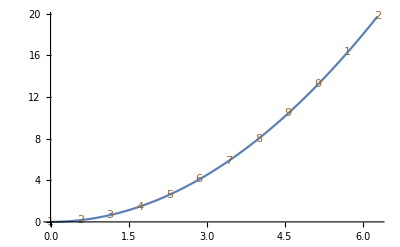
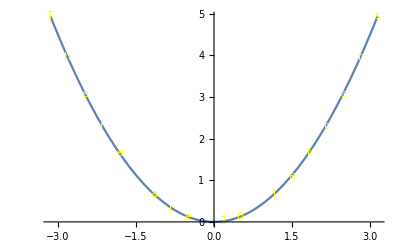
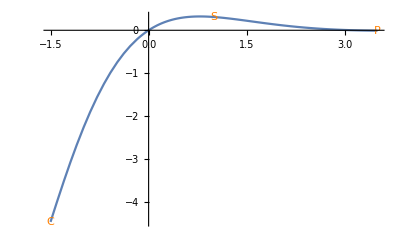
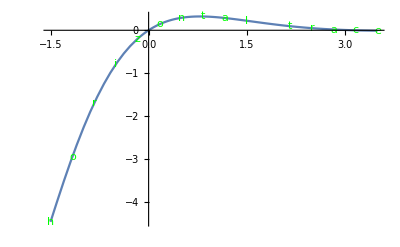
horizontalTrace | {hw4ffun,123456789012,0,2 π,RGBColor[0.6, 0.4, 0.2]} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
horizontalTrace | {hw4ffun,There are 20 letters,-π,π,RGBColor[1, 1, 0]} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
horizontalTrace | {hw4hfun,CSP,-1.5,3.5,RGBColor[1, 0.5, 0]} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}
horizontalTrace | {hw4hfun,horizontal trace,-1.5,3.5,RGBColor[0, 1, 0]} | {-Graphics-, < -- Correct COMPARE TO Student -->,-Graphics-}

```mathematica
(* since there are many different ways of accomplishing the required work most tests will not work for all solutions*)
(* in addition to the internal testing a visual comparison is needed to determine whether the items are the same *)
testHorizontalTrace[testHorizontalTraceCases, test4]
```

#### testing return values - for students verticalTrace

```mathematica
(* this is a list for the parameters for each of the funtion calls made during the test *)testVerticalTraceCases={{hw4ffun,"Parabola", 8, -1.5, 3, 10},{hw4gfun,"Cos", 8, 0, 2 π, 10}, {hw4kfun, "CPS", 10,0, 15/8  Pi, 15},{hw4mfun, "x^2", 10,2,6.3 , 15}};
```

```mathematica
(* since there are many different ways of accomplishing the required work most tests will not work for all solutions*)
(* in addition to the internal testing a visual comparison is needed to determine whether the items are the same *)
testVerticalTrace[ testVerticalTraceCases, test5]
```

Parabola

Parabola

Parabola

«5 more identical outputs»

leading Blnaks lists stud, corr{2,1,0,0,1,3,6,10} {2,1,0,0,1,3,6,10}

Cos

Cos

Cos

«5 more identical outputs»

leading Blnaks lists stud, corr{10,8,4,0,0,4,8,10} {10,8,4,0,0,4,8,10}

CPS

CPS

CPS

«7 more identical outputs»

leading Blnaks lists stud, corr{8,12,15,15,11,7,2,0,1,5} {8,12,15,15,11,7,2,0,1,5}

x^2

x^2

x^2

«7 more identical outputs»

leading Blnaks lists stud, corr{0,1,2,3,5,6,8,10,13,15} {0,1,2,3,5,6,8,10,13,15}

verticalTrace | {hw4ffun,Parabola,8,-1.5,3,10} | {
  Parabola
 Parabola
Parabola
Parabola
 Parabola
   Parabola
      Parabola
          Parabola
 < -- Correct COMPARE TO Student -->
  Parabola
 Parabola
Parabola
Parabola
 Parabola
   Parabola
      Parabola
          Parabola}
verticalTrace | {hw4gfun,Cos,8,0,2 π,10} | {
          Cos
        Cos
    Cos
Cos
Cos
    Cos
        Cos
          Cos
 < -- Correct COMPARE TO Student -->
          Cos
        Cos
    Cos
Cos
Cos
    Cos
        Cos
          Cos}
verticalTrace | {hw4kfun,CPS,10,0,(15 π)/8,15} | {
        CPS
            CPS
               CPS
               CPS
           CPS
       CPS
  CPS
CPS
 CPS
     CPS
 < -- Correct COMPARE TO Student -->
        CPS
            CPS
               CPS
               CPS
           CPS
       CPS
  CPS
CPS
 CPS
     CPS}
verticalTrace | {hw4mfun,x^2,10,2,6.3,15} | {
x^2
 x^2
  x^2
   x^2
     x^2
      x^2
        x^2
          x^2
             x^2
               x^2
 < -- Correct COMPARE TO Student -->
x^2
 x^2
  x^2
   x^2
     x^2
      x^2
        x^2
          x^2
             x^2
               x^2}